```mathematica
ClearAll["Global`*"]
$Assumptions={R∈Reals,V0∈Reals,x>0,E>0,t>0,E∈Reals,τ>0,α>0,β>0};
```

1

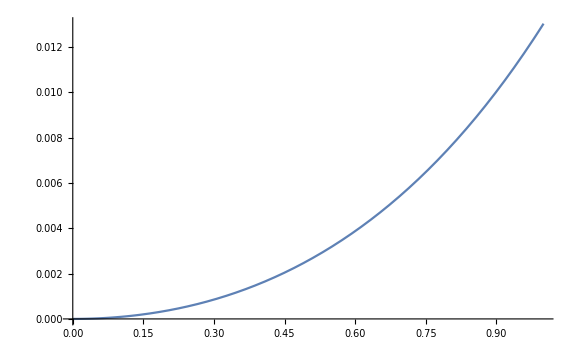

```mathematica
R[V0_]:= (Sqrt[E]-Sqrt[E-V0])^2/(Sqrt[E]+Sqrt[E-V0])^2;
Ri=1
Plot[{R[V0]},{V0,0,1}]
```